## All of the following is for a Maxwellian

#### Load package

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
```

```mathematica
(*Limit[LKMwellDensFac[phiBar,RB],RB->∞,Assumptions->phiBar>0]*)
(*1/2 ((2 √phiBar)/(√π)+ⅇ^phiBar Erfc[√phiBar])*)
```

```mathematica
dPhi=941;T=110;
```

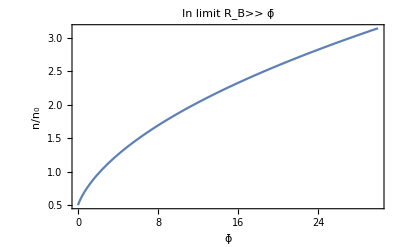

```mathematica
Plot[LKMwellDensFacRBInf[phiBar],{phiBar,0,30},PlotLabel->"In limit R_B>> ϕ̄",Frame->True,FrameLabel->{"ϕ̄","n/n_0"},FrameStyle->(FontSize->18)]
```

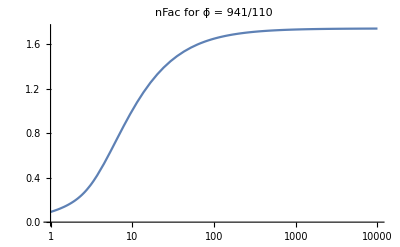

```mathematica
LogLinearPlot[LKMwellDensFac[dPhi/T,RB],{RB,1,10000},PlotLabel->"LKMwellDensFac for ϕ̄ = 941/110"]
```

```mathematica
dPhi=110;T=110;
```

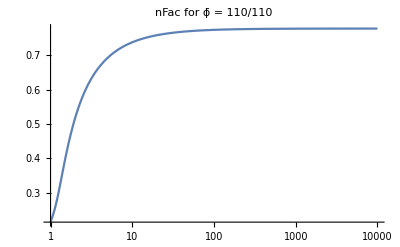

```mathematica
LogLinearPlot[LKMwellDensFac[dPhi/T,RB],{RB,1,10000},PlotLabel->StringForm["LKMwellDensFac for ϕ̄ = `1`/`2`",dPhi,T],PlotRange->All]
```

```mathematica
dPhi=10000;T=110;
```

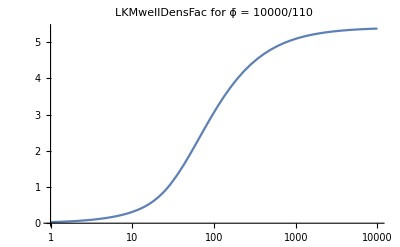

```mathematica
LogLinearPlot[LKMwellDensFac[dPhi/T,RB],{RB,1,10000},PlotLabel->StringForm["LKMwellDensFac for ϕ̄ = `1`/`2`",dPhi,T],PlotRange->All]
```